```mathematica
S[x_]:=4/(Sqrt[Pi W])Exp[-x^2/W]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1,Subscript[L, 1]->1}];
```

```mathematica
Subscript[T, -2][ξ_]:=Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ<Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[A, 0]},Assumptions->{ξ<Subscript[A, 0],W>0}]
Subscript[F, -2][ξ_]=Refine[Subscript[T, -2][ξ]/.var,ξ<Subscript[A, 0]<0];
Subscript[T, -1][ξ_]:=-Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+ D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ>Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0],Subscript[A, 0]<Subscript[L, 0]}/.var]+
Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0],Subscript[A, 0]<Subscript[L, 0],W>0}/.var]
Subscript[F, -1][ξ_]=Refine[Subscript[T, -1][ξ]/.var,{Subscript[A, 0]<ξ<Subscript[L, 0]}/.var];
Subscript[T, 1][ξ_]:=Limit[Subscript[c, 5] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ<Subscript[A, 1]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],Subscript[A, 1]}/.var,Assumptions->{Subscript[L, 1]<ξ<Subscript[A, 1],Subscript[L, 1]<Subscript[A, 1]}/.var]+
Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],Subscript[A, 1]}/.var,Assumptions->{Subscript[L, 1]<ξ<Subscript[A, 1],Subscript[L, 1]<Subscript[A, 1],W>0}/.var]
Subscript[F, 1][ξ_]=Refine[Subscript[T, 1][ξ]/.var,{Subscript[L, 1]<ξ<Subscript[A, 1]}/.var];
Subscript[T, 2][ξ_]:=-Limit[Subscript[c, 5] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ>Subscript[A, 1]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 1],∞},Assumptions->ξ>Subscript[A, 1]]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 1],∞},Assumptions->{ξ>Subscript[A, 1],W>0}]
Subscript[F, 2][ξ_]=Refine[Subscript[T, 2][ξ]/.var,0<Subscript[A, 1]<ξ];
```

```mathematica
Subscript[eqn, 1]=Subscript[F, -2][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[F, -1][Subscript[A, 0]]+1==0;
Subscript[eqn, 3]=Subscript[F, 1][Subscript[A, 1]]+1==0;
Subscript[eqn, 4]=Subscript[F, 2][Subscript[A, 1]]+1==0;
Subscript[eqn, 5]=Subscript[F, 1][Subscript[L, 1]]==0/.var;
```

```mathematica
Solve[{Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],-10<Subscript[c, 5]<0,1<Subscript[A, 1]<10,400<Q<500}/.{W->6},{Subscript[c, 5],Subscript[A, 1],Q}]
```

479.6330301017450990566760643348028897758680020950645046869878840989598468478901284486019763750921068

{c_0→4.1180165816993154026063346154672245551523861915903,c_5→-4.1180165816993154026063346154672245551523861915903,A_0→-1.4781779999055126643217274780315141278695362057708,A_1→1.4781779999055126643217274780315141278695362057708,Q→479.63303010174509905667606433480288977586800209506}

0. | 0.

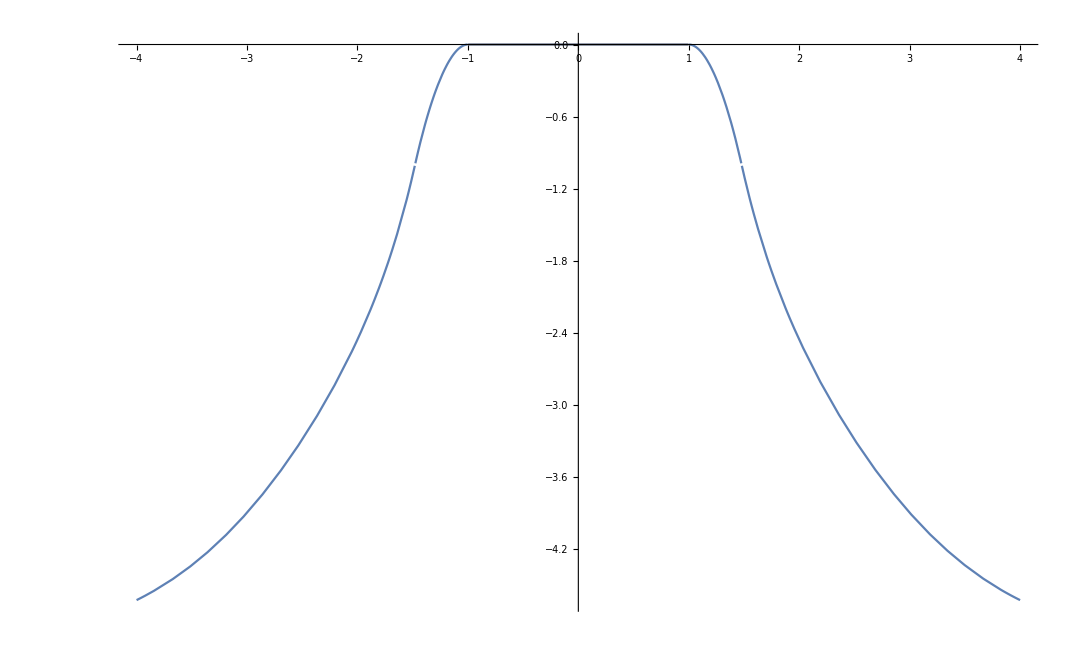

```mathematica
tempQ={W->Rationalize[6.0]};
sol=FindRoot[{Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 5],0},{Subscript[A, 0],-1.5},{Subscript[A, 1],1.5},{Q,470}},WorkingPrecision->50]
sol=Join[sol,tempQ,var];
funcList={{Subscript[F, 2][-x],x<Subscript[A, 0]},{Subscript[F, -1][x],Subscript[A, 0]<=x<Subscript[L, 0]},{Subscript[F, 1][x],Subscript[L, 1]<x<=Subscript[A, 1]},{Subscript[F, 2][x],Subscript[A, 1]<x}};
M[x_]=Piecewise[funcList/.sol];
Subscript[p, 1]=Plot[M[x],{x,-4,4}];
Subscript[p, 2]=Plot[0,{x,Subscript[L, 0],Subscript[L, 1]}/.var,PlotStyle->{Brown,Thick}];
Print[N[Subscript[F, -1][-1]/.sol]," | ",N[Subscript[F, 1][1]/.sol]];
Show[Subscript[p, 1],Subscript[p, 2],PlotRange->All]
```

```mathematica
NUM=12001;
points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];
sols={N[479.6330301017450990566760643348028897758680020950645046869878840989598468478901284486019763750921067903882617371515335`100.],N[M[0]/.sol],nSolution};
```

```mathematica
sols
```

{479.633,0.,{-4.97588,-4.97585,-4.97582,-4.97579,-4.97576,-4.97573,-4.9757,-4.97566,-4.97563,-4.9756,-4.97557,-4.97554,-4.97551,-4.97548,-4.97545,-4.97542,-4.97539,-4.97536,-4.97532,-4.97529,-4.97526,-4.97523,11957,-4.97523,-4.97526,-4.97529,-4.97532,-4.97536,-4.97539,-4.97542,-4.97545,-4.97548,-4.97551,-4.97554,-4.97557,-4.9756,-4.97563,-4.97566,-4.9757,-4.97573,-4.97576,-4.97579,-4.97582,-4.97585,-4.97588}}
 |  |  |  |

```mathematica
Export["C:\\masterA GitHub\\Code\\Gaussian\\Std 6\\LimitingCase.csv",sols,Format->Table];
```